## Eigenvalues

```mathematica
lines1S2SL0=<|"4"->Import["lines/unequalM_1P1D_L1_dim8.mx"],"10"->Import["lines/unequalM_1P1D_L1_dim20.mx"],"20"->Import["lines/unequalM_1P1D_L1_dim40.mx"],"horizontalLine"->Table[{omega,6.99634},{omega,0.5,2.5,0.5}]|>;
```

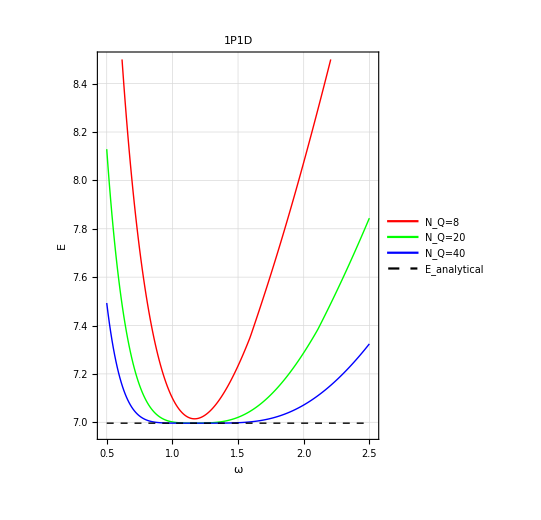

```mathematica
eigenvaluePlot=ListPlot[{lines1S2SL0["4"],lines1S2SL0["10"],lines1S2SL0["20"],lines1S2SL0["horizontalLine"]},
AspectRatio->1.3,Joined->True,PlotStyle->{{Red,Thick},{Green,Thick},{Blue,Thick},{Black,Dashed,Thick}},LabelStyle->{FontSize->16,FontFamily->"Times",Black},Frame->{{True,True},{True,True}},
GridLines->Automatic,
FrameLabel->{{"E",None},{"ω",None}},
PlotLabel->"1P1D",
PlotTheme->"Detailed",PlotLegends->Placed[{"N_Q=8","N_Q=20","N_Q=40","E_analytical"},{Center,Top}],PlotRange->{{0.47,2.53},{6.96,8.5}}]
```

```mathematica
Export["plots/unequalM_1P1D_L1.pdf",eigenvaluePlot,"PDF","AllowRasterization"->False]
```

plots/unequalM_1P1D_L1.pdf

## Eigenvectors

```mathematica
vectors=<|"1"->Import["lines/vector_components/equalM_1S1S_dim4.mx"],
"2"->Import["lines/vector_components/equalM_1S1S_dim10.mx"],
"3"->Import["lines/vector_components/equalM_1S1S_dim20.mx"],
"horizontal"->Table[{omega,1},{omega,0.5,2.5,0.5}]|>;
```

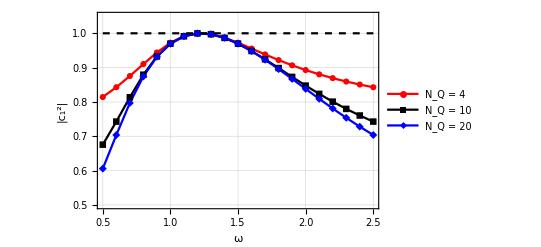

```mathematica
xaxis10S={"1S1S","1S2S","1P1P","2S1S","1S3S","1P2P","1D1D","2S2S","2P1P","3S1S"};
eigenvectorPlot=ListPlot[
{vectors["1"],vectors["2"],vectors["3"],vectors["horizontal"]},
Joined->True,
(*FrameTicks->{{Automatic,None}, {Transpose[{Range[10],xaxis10S}],None}},*)
FrameTicks->{{Automatic,None}, {Automatic,None}},
AxesOrigin->{0.5,0},
LabelStyle->{FontSize->12, FontFamily->"Times",Black},
Frame->{{True,True},{True,True}},
(*PlotRange->{{0.7,10.2},{0,1}},*)
PlotRange->{0.5,1.05},
PlotStyle->{Red,Black,Blue,{Black,Dashed}},
FrameStyle->Thickness->0.0055,
(*Filling->Axis,*)
PlotLegends->Placed[{Style["N_Q = 4",FontSize->14,FontFamily->"Times"],Style["N_Q = 10",FontSize->14,FontFamily->"Times"],
Style["N_Q = 20",FontSize->14,FontFamily->"Times"]},{Center,Bottom}],
GridLines->Automatic,
GridLinesStyle->Directive[Gray,Dashed,Thickness->0.0005],
FrameLabel->{{"|c_1^2|",None},{"ω",None}},
PlotMarkers->{Automatic,Automatic,Automatic,None}
]
```

```mathematica
Export["plots/vector_components/equalM_1S1S.pdf",eigenvectorPlot,"PDF","AllowRasterization"->False]
```

plots/vector_components/equalM_1S1S.pdf

## Expectation Values

```mathematica
expValues=<|"0"->Import["lines/expValues/RMS_rho2_equalM_1S1S_dim4.mx"],"1"->Import["lines/expValues/RMS_rho2_equalM_1S1S_dim10.mx"],
"2"->Import["lines/expValues/RMS_rho2_equalM_1S1S_dim20.mx"],
"horizontal"->Table[{omega,1.56508},{omega,0.5,2,0.5}],
"vertical"->Table[{√(3/2),y},{y,1.5,1.62,0.1}]|>;
```

```mathematica
expValues["2"]
```

{{0.5,0.692895},{0.6,0.767862},{0.7,0.867552},{0.8,0.98204},{0.9,1.10258},{1.,1.22477},{1.1,1.34722},{1.2,1.46969},{1.3,1.59217},{1.4,1.71464},{1.5,1.83709},{1.6,1.95939},{1.7,2.08126},{1.8,2.20214},{1.9,2.32128},{2.,2.43779}}

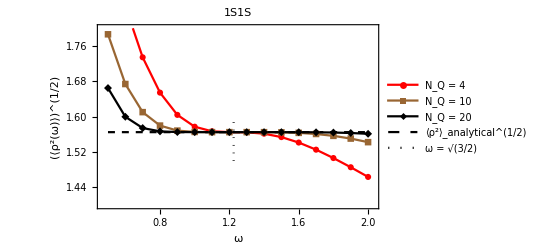

```mathematica
expValuePlot=ListPlot[{expValues["0"],expValues["1"],expValues["2"],expValues["horizontal"],expValues["vertical"]},
Joined->True,
Frame->{{True,True},{True,True}},
FrameStyle->Thickness->0.0055,
FrameLabel->{{"(⟨ρ^2(ω)⟩)^(1/2)",None},{"ω",None}},
FrameTicks->{{Automatic,None}, {Automatic,None}},
LabelStyle->{FontSize->12, FontFamily->"Times",Black},
(*Filling->2.44949,*)
PlotRange->{{0.47,2.03},{1.4,1.8}},
PlotLegends->{Placed[{Style["N_Q = 4",FontSize->13,FontFamily->"Times"],Style["N_Q = 10",FontSize->13,FontFamily->"Times"],
Style["N_Q = 20",FontSize->13,FontFamily->"Times"]},{Right,Top}],
Placed[{None,None,None,Style["⟨ρ^2⟩_analytical^(1/2)",FontSize->13,FontFamily->"Times"],Style["ω = √(3/2)",FontSize->13,FontFamily->"Times"]},{Left,Bottom}]},
PlotStyle->{{Red},{Brown},{Black},{Black,Dashed},{Black,Dotted}},
PlotLabel->"1S1S",
PlotMarkers->{Automatic,Automatic,Automatic,None,None}
]
```

```mathematica
Export["plots/expValues/equalM_rmsRho2_1S1S.pdf",expValuePlot,"PDF","AllowRasterization"->False]
```

plots/expValues/equalM_rmsRho2_1S1S.pdf

## Component of Eigenvector

```mathematica
ListPlot[{line1,line2,line3,line4,horizontal},Joined->True,PlotMarkers->Automatic,
PlotRange->{0.4,1.02}]
```